```mathematica
q0=4.80320425*10^(-10);
epsilon=300.0;
nd0=2.0*10^11;
nd1=2.0*10^11;
kb=1.381*10^(-16);
tem=298.0;
deltapot=kb*tem*Log[nd1/nd0]/q0;
debyel0=1/Sqrt[4*π*q0^2*nd0/(epsilon*kb*tem)];
debyel1=1/Sqrt[4*π*q0^2*nd1/(epsilon*kb*tem)];
pot=NDSolve[{-y''[x]==(4*π*q0/epsilon)*nd0*(1-Exp[q0*y[x]/(kb*tem)]),y[0]==-0.1*kb*tem/q0,y'[0]==-0.1*kb*tem/(q0*debyel0)},y[x],{x,0,5*10^(-5)}];
potential0[x_]=Evaluate[y[x]/.pot][[1]];
dpot0[x_]=D[potential0[x],x];
rho0[x_]=-epsilon*D[D[potential0[x],x],x]/(4*π*q0);
```

```mathematica
debyel0
```

1.4592×10^-6

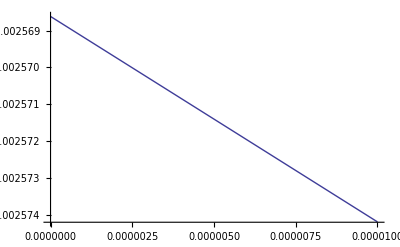

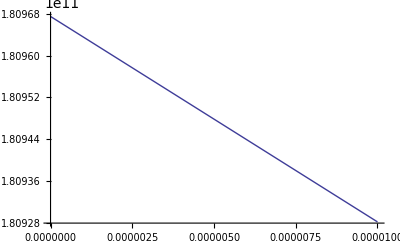

```mathematica
p0=Plot[299.792458*potential0[x],{x,0,10*10^(-6)},PlotRange->All]
charge0[x_]=1.0*(nd0-nd0*Exp[q0*potential0[x]/(kb*tem)]);
carrier0[x_]=nd0-charge0[x];
p00=Plot[carrier0[x],{x,0,10*10^(-6)},PlotRange->All]
```

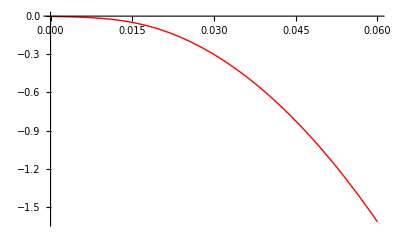

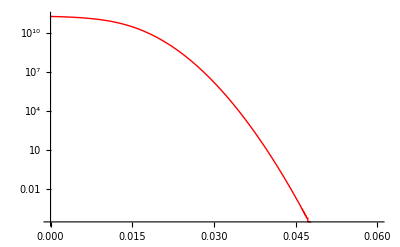

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.×10^-7, 6.35731×10^-6}}.

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5.13242×10^-9}}.

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.×10^-7, 6.35731×10^-6}}.

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5.13242×10^-9}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5.13242×10^-9}}.

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.×10^-7, 6.35731×10^-6}}.

NIntegrate::inumr: The integrand 1/8.01×10^-19\ (2.×10^11 - 1.\ (2.×10^11 - 2.×10^11\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5.13242×10^-9}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
x0=0.2*10^(-6);
totalcharge0=NIntegrate[charge0[x],{x,0,x0}];
depth=60000*10^(-6);
pot1=NDSolve[{-y''[x]==(4*π*q0/epsilon)*(nd1-nd0*Exp[q0*y[x]/(kb*tem)]),y[x0]==potential0[x0],y'[x0]==dpot0[x0]},y[x],{x,x0,x0+depth}];
potential1[x_]=Evaluate[y[x]/.pot1][[1]];
p1=Plot[299.792458*potential1[x],{x,x0,x0+depth},PlotRange->All,PlotStyle->RGBColor[1,0,0]];
p2=Plot[299.792458*potential0[x],{x,0,x0},PlotRange->All];
charge1[x_]=1.0*(nd1-nd0*Exp[q0*potential1[x]/(kb*tem)]);
carrier1[x_]=nd1-charge1[x];
totalcharge1=NIntegrate[charge1[x],{x,x0,x0+depth}];
p3=LogPlot[carrier1[x],{x,x0,x0+depth},PlotRange->All,PlotStyle->RGBColor[1,0,0]];
p4=LogPlot[carrier0[x],{x,0,x0},PlotRange->All];
Show[p1,p2]
Show[p3,p4]
mu=5.0;
epsilon0si=8.854187817*10^(-14);
q0si=1.602*10^(-19);
imp1[x_,omega_]=1/(q0si*mu*carrier1[x]+ⅈ*2*π*epsilon*epsilon0si*omega);
imp0[x_,omega_]=1/(q0si*mu*carrier0[x]+ⅈ*2*π*epsilon*epsilon0si*omega);
totalimp1[omega_]=NIntegrate[imp1[x,omega],{x,x0,x0+depth}];
totalimp0[omega_]=NIntegrate[imp0[x,omega],{x,0,x0}];
totalimp[omega_]=totalimp0[omega]+totalimp1[omega];
apparentc[omega_]=Im[1/totalimp[omega]]/(2*π*omega);
```

```mathematica
-299.792458*potential1[x0+depth]
totalimp[10000]
apparentc[10000]
```

1.61887

519.211-35917.8 ⅈ

4.43017×10^-10

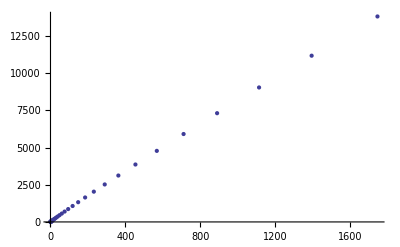

```mathematica
msplot=Table[{Re[totalimp[10^t]],-Im[totalimp[10^t]]},{t,0,4,0.1}];
ListPlot[msplot,PlotRange->All]
```

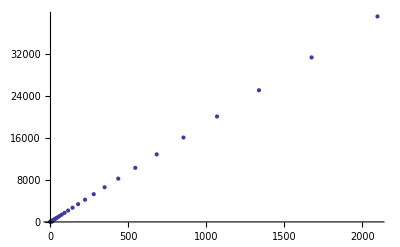

```mathematica
msplot1=Table[{Re[totalimp1[10^t]],-Im[totalimp1[10^t]]},{t,0,4,0.1}];
ListPlot[msplot1,PlotRange->All]
```

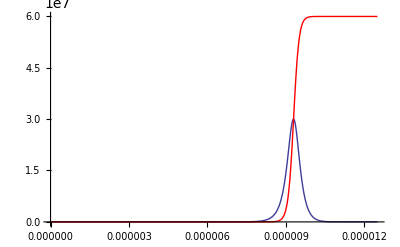

```mathematica
omega0=100;
p5=Plot[Re[imp1[x,omega0]],{x,x0,x0+depth},PlotRange->All];
p6=Plot[-Im[imp1[x,omega0]],{x,x0,x0+depth},PlotRange->All,PlotStyle->RGBColor[1,0,0]];
p7=Plot[Re[imp0[x,omega0]],{x,0,x0},PlotRange->All];
p8=Plot[-Im[imp0[x,omega0]],{x,0,x0},PlotRange->All,PlotStyle->RGBColor[1,0,0]];
Show[p5,p6,p7,p8]
```

NIntegrate::inumr: The integrand 1/3.204×10^-19\ (2.9×10^18 - 1.\ (2.9×10^18 - 2.9×10^18\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.49137×10^-10}}.

NIntegrate::inumr: The integrand 1/3.204×10^-19\ (2.9×10^18 - 1.\ (2.9×10^18 - 2.9×10^18\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.×10^-7, 2.00146×10^-7}}.

NIntegrate::inumr: The integrand 1/3.204×10^-19\ (2.9×10^18 - 1.\ (2.9×10^18 - 2.9×10^18\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.49137×10^-10}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000117769}. NIntegrate obtained 7.81719×10^6 - 2.71156×10^7\ ⅈ and 866.067 for the integral and error estimates.

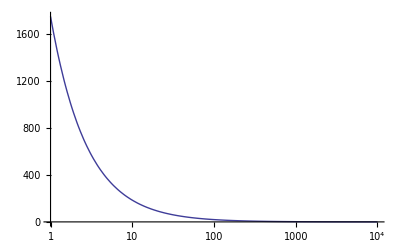

```mathematica
LogLinearPlot[Re[totalimp[omega]],{omega,1,10000},PlotRange->All]
```

NIntegrate::inumr: The integrand 1/3.204×10^-19\ (2.9×10^18 - 1.\ (2.9×10^18 - 2.9×10^18\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.49137×10^-10}}.

NIntegrate::inumr: The integrand 1/3.204×10^-19\ (2.9×10^18 - 1.\ (2.9×10^18 - 2.9×10^18\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.×10^-7, 2.00146×10^-7}}.

NIntegrate::inumr: The integrand 1/3.204×10^-19\ (2.9×10^18 - 1.\ (2.9×10^18 - 2.9×10^18\ Power[« 2 »])) + (0.  + 1.66898×10^-10\ ⅈ)\ omega
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.49137×10^-10}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000117769}. NIntegrate obtained 7.81719×10^6 - 2.71156×10^7\ ⅈ and 866.067 for the integral and error estimates.

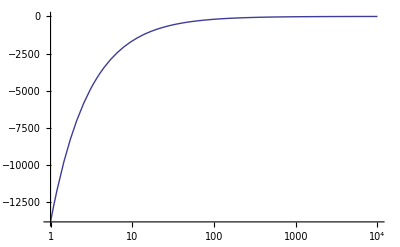

```mathematica
LogLinearPlot[Im[totalimp[omega]],{omega,1,10000},PlotRange->All]
```